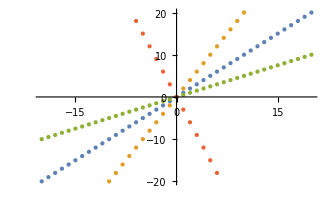

```mathematica
ListPlot[{Table[{n,n},{n,-20,20}],Table[{n,2n},{n,-10,10}],Table[{n,0.5n},{n,-20,20}],Table[{n,-3n},{n,-6,6}]}]
```

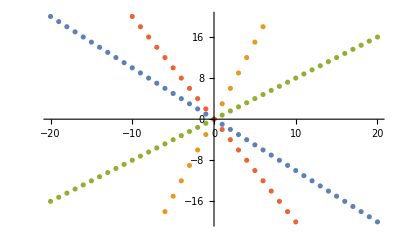

```mathematica
ListPlot[{Table[{n,-n},{n,-20,20}],Table[{n,3n},{n,-6,6}],Table[{n,0.8n},{n,-20,20}],Table[{n,-2n},{n,-10,10}]}]
```

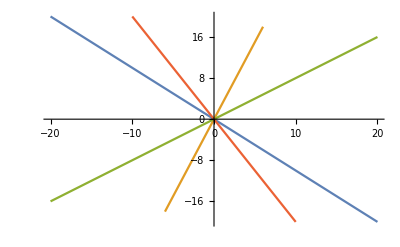

```mathematica
ListLinePlot[{Table[{n,-n},{n,-20,20}],Table[{n,3 n},{n,-6,6}],Table[{n,0.8 n},{n,-20,20}],Table[{n,-2 n},{n,-10,10}]}]
```

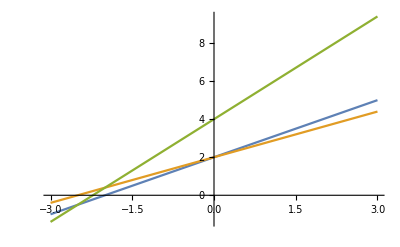

```mathematica
Plot[{x+2,0.8x+2,1.8x+4},{x,-3,3}]
```

```mathematica
data={{1,0,1},{2,1,2},{-1,1,-1}};

Graphics3D[{Arrow[{{0,0,0},#}]&/@data,InfinitePlane[{{1,0,1},{2,1,2},{-1,1,-1}}]}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Arrow[{{0,0,0},{1,0,1}}],Arrow[{{0,0,0},{2,1,2}}],Arrow[{{0,0,0},{-1,1,-1}}]},InfinitePlane[{{1,0,1},{2,1,2},{-1,1,-1}}]}],Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Arrow[{{0,0,0},{1,0,1}}],Arrow[{{0,0,0},{2,1,2}}],Arrow[{{0,0,0},{-1,1,-1}}]},InfinitePlane[{{1,0,1},{2,1,2},{-1,1,-1}}]},{Lighting->"Neutral"}],Axes->True]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Arrow[{{0,0,0},{1,0,1}}],Arrow[{{0,0,0},{2,1,2}}],Arrow[{{0,0,0},{-1,1,-1}}]},InfinitePlane[{{1,0,1},{2,1,2},{-1,1,-1}}]}],ViewPoint->{0,0,-∞}]
```

```mathematica
data={{1,1,1},{2,0,1},{3,1,2},{7,3,5}};

Graphics3D[{Arrow[{{0,0,0},#}]&/@data,InfinitePlane[{{1,1,1},{2,0,1},{3,1,2}}]}]
```

-Graphics3D-

```mathematica
data={{1,1,0},{-1,0,1}};

Graphics3D[{Arrow[{{0,0,0},#}]&/@data,InfinitePlane[{{1,1,0},{-1,0,1}}]}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Arrow[{{0,0,0},{1,1,0}}],Arrow[{{0,0,0},{-1,0,1}}]},InfinitePlane[{0,0,0},{{1,1,0},{-1,0,1}}]}],Axes->True]
```

-Graphics3D-